# The Lagrangian Method

This notebook demonstrates chapter 6 of the David Morin’s book (morin@physics.harvard.edu).

## A mass on the end of a spring (a harmonic oscillator)

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

Kinetic energy is defined as T
Potential energy is defined as V
Lagrangian is defined as L=T-V

```mathematica
T = 1/2*m*x'[t]^2
```

1/2 m x'[t]^2

```mathematica
V = 1/2*k*x[t]^2
```

1/2 k x[t]^2

```mathematica
L = T-V
```

-1/2 k x[t]^2+1/2 m x'[t]^2

Now, we calculate: d/dt((∂L)/(∂x'(t)))=(∂L)/(∂x)

```mathematica
D[D[L,x'[t]],t]==D[L,x[t]]
```

m x''[t]==-k x[t]

## The spring pendulum

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

First, we write down the equation of the kinetic energy which comes from tangential and radial motions:
T=radial + tangential
T=1/2 m(ẋ)^2+1/2 m((l+x)((OverDot[θ)]))^2

```mathematica
T=1/2*m*x'[t]^2+1/2*m*((l+x[t])*θ'[t])^2
```

1/2 m x'[t]^2+1/2 m (l+x[t])^2 θ'[t]^2

Next, we write down the potential energy, which come from the gravity and from the spring. As for the energy that comes from the gravity, we shall compute it from the origin of the spring (also for simplification). Therefore, we put negative sign as its direction is now reversed.

```mathematica
V=-m*g*(l+x[t])*Cos[θ[t]]+1/2*k*x[t]^2
```

1/2 k x[t]^2-g m Cos[θ[t]] (l+x[t])

Thus, the Lagrangian can now be written as:

```mathematica
L=T-V
```

-1/2 k x[t]^2+g m Cos[θ[t]] (l+x[t])+1/2 m x'[t]^2+1/2 m (l+x[t])^2 θ'[t]^2

Now, we calculate: d/dt((∂L)/(∂x'(t)))=(∂L)/(∂x)

```mathematica
D[D[L,x'[t]],t]==D[L,x[t]]
```

m x''[t]==g m Cos[θ[t]]-k x[t]+m (l+x[t]) θ'[t]^2

```mathematica
Solve[%,x''[t]]
```

{{x''[t]→(g m Cos[θ[t]]-k x[t]+l m θ'[t]^2+m x[t] θ'[t]^2)/m}}

Since there are two variables: θ (tangential) and x(radial), we also need to find: d/dt((∂L)/(∂θ'(t)))=(∂L)/(∂θ)

```mathematica
D[D[L,θ'[t]],t]==D[L,θ[t]]
```

2 m (l+x[t]) x'[t] θ'[t]+m (l+x[t])^2 θ''[t]==-g m Sin[θ[t]] (l+x[t])

```mathematica
Simplify[%]
```

m (l+x[t]) (g Sin[θ[t]]+2 x'[t] θ'[t]+(l+x[t]) θ''[t])==0

```mathematica
Solve[%,θ''[t]]
```

{{θ''[t]→(-g Sin[θ[t]]-2 x'[t] θ'[t])/(l+x[t])}}

## Forces of constraints

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

-Graphics-
A particle is sliding off a fixed frictionless hemisphere of radius R.
We will start with finding L=T-K.

```mathematica
T=1/2*m*(R*θ'[t])^2
```

1/2 m R^2 θ'[t]^2

```mathematica
V = m*g*R*Cos[θ[t]]
```

g m R Cos[θ[t]]

```mathematica
L=T-V
```

-g m R Cos[θ[t]]+1/2 m R^2 θ'[t]^2

Next, we find: d/dt((∂L)/(∂θ'(t)))=(∂L)/(∂θ)

```mathematica
D[D[L,θ'[t]],t]==D[L,θ[t]]
```

m R^2 θ''[t]==g m R Sin[θ[t]]

```mathematica
Solve[%, θ''[t]]
```

{{θ''[t]→(g Sin[θ[t]])/R}}

## Moving plane

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

-Graphics-

FIrst we calculate the kinetic energy. When moving, let’s say the speed of M is VM and the speed of m is Vm . Vm has two components, in x and in y direction. vmy has negative sign as it is moving downward.

```mathematica
VM = a'[t];
vmx= a'[t]+b'[t]*Cos[θ];
vmy= -b'[t]*Sin[θ];
```

Next, we can derive the kinetic energy as

```mathematica
T=1/2*M*VM^2+1/2*m*vmx^2+1/2*m*vmy^2
```

1/2 M a'[t]^2+1/2 m Sin[θ]^2 b'[t]^2+1/2 m (a'[t]+Cos[θ] b'[t])^2

```mathematica
Simplify[T]
```

1/2 ((m+M) a'[t]^2+2 m Cos[θ] a'[t] b'[t]+m b'[t]^2)

The potential energy can be derived as:

```mathematica
V =-m*g*b[t]*Sin[θ]
```

-g m b[t] Sin[θ]

The Lagrangian can be calculated as:

```mathematica
L=T-V
```

g m b[t] Sin[θ]+1/2 M a'[t]^2+1/2 m Sin[θ]^2 b'[t]^2+1/2 m (a'[t]+Cos[θ] b'[t])^2

```mathematica
Simplify[L]
```

1/2 (2 g m b[t] Sin[θ]+(m+M) a'[t]^2+2 m Cos[θ] a'[t] b'[t]+m b'[t]^2)

```mathematica
eq1:=D[D[L,a'[t]],t]==D[L,a[t]]
```

```mathematica
eq2:=D[D[L,b'[t]],t]==D[L,b[t]]
```

```mathematica
eq1
```

M a''[t]+m (a''[t]+Cos[θ] b''[t])==0

```mathematica
eq2
```

m Sin[θ]^2 b''[t]+m Cos[θ] (a''[t]+Cos[θ] b''[t])==g m Sin[θ]

```mathematica
Simplify[eq2]
```

m (Cos[θ] a''[t]+b''[t])==g m Sin[θ]

The Lagrangian gives s two equations that we need to solve:

```mathematica
Solve[{eq1, eq2}, {a''[t],b''[t]}]
```

{{a''[t]→-(g m Cos[θ] Sin[θ])/(M Cos[θ]^2+m Sin[θ]^2+M Sin[θ]^2),b''[t]→(g (m+M) Sin[θ])/(M Cos[θ]^2+m Sin[θ]^2+M Sin[θ]^2)}}

```mathematica
Simplify[%]
```

{{a''[t]→(g m Sin[2 θ])/(-m-2 M+m Cos[2 θ]),b''[t]→(2 g (m+M) Sin[θ])/(m+2 M-m Cos[2 θ])}}

## Two falling sticks

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

-Graphics-
-Graphics-

Position of the bottom mass:

```mathematica
p1x=r*Sin[θ1[t]];
p1y=r*Cos[θ1[t]];
p2x=2*r*Sin[θ1[t]]-r*Sin[θ2[t]];
p2y=2*r*Cos[θ1[t]]+r*Cos[θ2[t]];
v2x = D[p2x,t];
v2y = D[p2y,t];
```

The potential energy:

```mathematica
V=m*g*p1y+m*g*p2y
```

g m r Cos[θ1[t]]+g m (2 r Cos[θ1[t]]+r Cos[θ2[t]])

```mathematica
K = Simplify[V]
```

g m r (3 Cos[θ1[t]]+Cos[θ2[t]])

Small angle approximation: cos(θ)=1-θ^2/2

```mathematica
V=V/.{Cos[θ1[t]]->(1-1/2*θ1[t]^2), Cos[θ2[t]]->(1-1/2*θ2[t]^2)}
```

g m r (1-θ1[t]^2/2)+g m (2 r (1-θ1[t]^2/2)+r (1-θ2[t]^2/2))

For the kinetic energy, we assume only rotation occurs for the bottom link, and only translation occurs at the top link.

```mathematica
T1=1/2*m*r^2*θ1'[t]^2; (* Bottom link *)
T2=1/2*m*(v2x^2+v2y^2); (* Top link *)
T2 = T2 /.{Sin[θ1[t]]->0,Sin[θ2[t]]->0,Cos[θ1[t]]->1,Cos[θ2[t]]->1};
T = T1+T2
```

1/2 m r^2 θ1'[t]^2+1/2 m (2 r θ1'[t]-r θ2'[t])^2

The Lagrangian:

```mathematica
L = T-V;
eq1:= D[D[L,θ1'[t]],t]==D[L,θ1[t]];
eq2:= D[D[L,θ2'[t]],t]==D[L,θ2[t]];
Simplify[eq1]
Simplify[eq2]
```

m r (3 g θ1[t]-5 r θ1''[t]+2 r θ2''[t])==0

m r (g θ2[t]+2 r θ1''[t]-r θ2''[t])==0

## Pendulum with an oscillating support

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

-Graphics-
-Graphics-
We ignore the fact that the particle of mass has rotation.

```mathematica
px=x[t]+l*Sin[θ[t]];
py = -l*Cos[θ[t]];
vx = D[px, t];
vy = D[py, t];
V = -m*g*l*Cos[θ[t]]; (* Potential enenrgy *)
T= 1/2*m* (vx^2+vy^2); (* Kinetic energy, with no rotation *)
```

```mathematica
Simplify[T]
```

1/2 m (x'[t]^2+2 l Cos[θ[t]] x'[t] θ'[t]+l^2 θ'[t]^2)

The Lagrangian is:

```mathematica
L= T-V
```

g l m Cos[θ[t]]+1/2 m (l^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+l Cos[θ[t]] θ'[t])^2)

```mathematica
eq := Simplify[D[D[L,θ'[t]],t]==D[L,θ[t]]]
```

```mathematica
eqr := Refine[eq, x''[t] = D[D[A*Cos[ω*t], t],t]]
eqr
```

l m (-A ω^2 Cos[t ω] Cos[θ[t]]+g Sin[θ[t]]+l θ''[t])==0

```mathematica
Solve[%, θ''[t]]
```

{{θ''[t]→(A ω^2 Cos[t ω] Cos[θ[t]]-g Sin[θ[t]])/l}}

## Two masses, one swinging

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

-Graphics-

```mathematica
V=M*g*r[t]-m*g*r[t]*Cos[θ[t]];
K=1/2*M*r'[t]^2+1/2*m*(r'[t]^2+r[t]^2*θ'[t]^2);
L=K-V
```

-g M r[t]+g m Cos[θ[t]] r[t]+1/2 M r'[t]^2+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
eq1:=Simplify[D[D[L,θ'[t]],t]==D[L,θ[t]]]
```

```mathematica
eq2:=Simplify[D[D[L,r'[t]],t]==D[L,r[t]]]
```

```mathematica
Solve[{eq1, eq2}, {θ''[t],r''[t]}]
```

{{θ''[t]→(-g Sin[θ[t]]-2 r'[t] θ'[t])/r[t],r''[t]→(-g M+g m Cos[θ[t]]+m r[t] θ'[t]^2)/(m+M)}}

```mathematica
g=9.8;
M=1;
m=1;
```

```mathematica
s=NDSolve[{eq1,eq2, θ[0]==0.1, θ'[0]==0, r[0]==1, r'[0]==0},{r, θ},{t,0,100}, MaxSteps->∞]
```

{{r→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

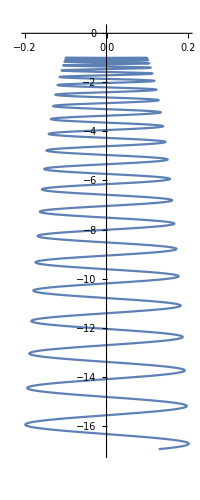

```mathematica
ParametricPlot[Evaluate[r[t]{Cos[θ[t]-π/2],Sin[θ[t]-π/2]}/.s],{t,0,100},Axes->True]
```

## Inverted pendulum

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

Position of the pendulum:

```mathematica
px = l*Sin[θ[t]];
py=y[t]+l*Cos[θ[t]];
```

The potential energy:

```mathematica
V=m*g*py
```

g m (l Cos[θ[t]]+y[t])

The kinetic energy:

```mathematica
vx = D[px,t];
vy = D[py,t];
T = 1/2*m*(vx^2+vy^2)
```

1/2 m (l^2 Cos[θ[t]]^2 θ'[t]^2+(y'[t]-l Sin[θ[t]] θ'[t])^2)

```mathematica
Simplify[T]
```

1/2 m (y'[t]^2-2 l Sin[θ[t]] y'[t] θ'[t]+l^2 θ'[t]^2)

The Lagrangian:

```mathematica
L = T-V
```

-g m (l Cos[θ[t]]+y[t])+1/2 m (l^2 Cos[θ[t]]^2 θ'[t]^2+(y'[t]-l Sin[θ[t]] θ'[t])^2)

```mathematica
eq=Simplify[D[D[L,θ'[t]],t]==D[L,θ[t]]]
```

l^2 m θ''[t]==l m Sin[θ[t]] (g+y''[t])

```mathematica
eq = Refine[eq, y''[t]=D[D[A*Cos[ω*t],t],t]]
```

l^2 m θ''[t]==l m (g-A ω^2 Cos[t ω]) Sin[θ[t]]

For small angle sin(θ)=θ:

```mathematica
eq = eq/.{Sin[θ[t]]->θ[t]}
```

l^2 m θ''[t]==l m (g-A ω^2 Cos[t ω]) θ[t]

```mathematica
eq = Solve[eq,θ''[t]]/.Rule->Equal
```

{{θ''[t]==((g-A ω^2 Cos[t ω]) θ[t])/l}}

## Normal force from a plane

```mathematica
Remove[Evaluate[$Context<>"*"]];
```

z is the normal distance from the mass to the plane (=0)
C[z] is the steep potential by the constraint

```mathematica
z=x[t]*Sin[θ]+y[t]*Cos[θ]
V=m*g*y[t]+C[z]
T = 1/2*m*(x'[t]^2+y'[t]^2)
L= T-V
```

Sin[θ] x[t]+Cos[θ] y[t]

C[Sin[θ] x[t]+Cos[θ] y[t]]+g m y[t]

1/2 m (x'[t]^2+y'[t]^2)

-C[Sin[θ] x[t]+Cos[θ] y[t]]-g m y[t]+1/2 m (x'[t]^2+y'[t]^2)

We need 3 equations for 3 unknowns: x''[t], y''[t], and C'[0]

```mathematica
eq1 = D[D[L,x'[t]],t]==D[L,x[t]]
```

m x''[t]==-Sin[θ] C'[Sin[θ] x[t]+Cos[θ] y[t]]

```mathematica
eq2= D[D[L,y'[t]],t]==D[L,y[t]]
```

m y''[t]==-g m-Cos[θ] C'[Sin[θ] x[t]+Cos[θ] y[t]]

Let’s find C[0] (calculated at z=0):

```mathematica
eq3 = Solve[z==0, x[t]]/.Rule->Equal
```

{{x[t]==-Cot[θ] y[t]}}

```mathematica
eq3 = D[D[eq3, t],t]
```

{{x''[t]==-Cot[θ] y''[t]}}

Now, we can find x''[t], y''[t], and C'[0]

```mathematica
sol = Simplify[Solve[{eq1, eq2, Part[eq3,1,1]}, {x''[t], y''[t], C'[Sin[θ] x[t]+Cos[θ] y[t]]}]]/.Rule->Equal
```

{{x''[t]==g Cos[θ] Sin[θ],y''[t]==-g Sin[θ]^2,C'[Sin[θ] x[t]+Cos[θ] y[t]]==-g m Cos[θ]}}

The normal force along the plane is: -C[0]=g m Cos[θ]